```mathematica
DOCLEN = 1000
```

1000

```mathematica
L1 = 50
```

50

```mathematica
L2 = 200
```

200

```mathematica
minJac[x_,n_,l_] := (n - 2l - x + 2)/(x + n)
```

```mathematica
maxJac[x_,n_,l_] := (n - l + 1 - x)/(x + n - l + 1)
```

```mathematica
minJac[200,1000,40]
```

361/600

```mathematica
edsim[x_,n_] := (n -x)/n
```

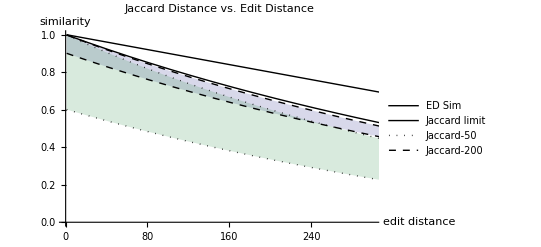

```mathematica
Plot[{maxJac[x,DOCLEN,L1],minJac[x,DOCLEN,L1],edsim[x,DOCLEN],maxJac[x,DOCLEN,L2],minJac[x,DOCLEN,L2],(DOCLEN - x)/(DOCLEN + x)},{x,1,DOCLEN}, PlotLegends-> LineLegend[{Thick,Black,Dotted,Dashed},{"ED Sim","Jaccard limit","Jaccard-50","Jaccard-200"}],PlotRange->{{0,300},{0,1}},ImageSize-> Scaled[.9], Filling->{1->{2}, 4->{5}}, PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Thick},{Black,Dotted},{Black,Dotted}, Black},AxesLabel->{"edit distance","similarity"}, PlotLabel->"Jaccard Distance vs. Edit Distance"]
```

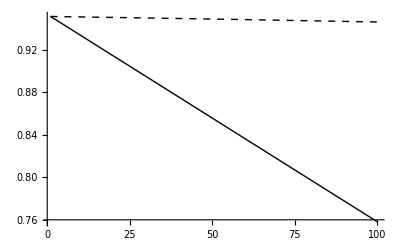

```mathematica
Plot[{maxJac[25,DOCLEN,x],minJac[25,DOCLEN,x]},{x,1,100},PlotStyle->{{Black,Dashed},{Black,Thick}}]
```

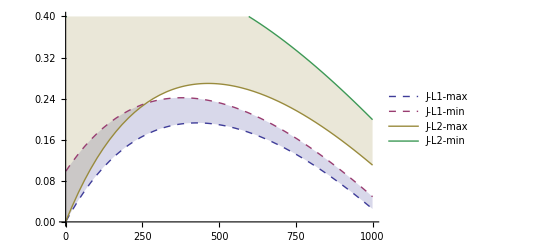

```mathematica
Plot[{edsim[x,DOCLEN] - maxJac[x,DOCLEN,L1],edsim[x,DOCLEN] - minJac[x,DOCLEN,L1],edsim[x,DOCLEN] - maxJac[x,DOCLEN,L2],edsim[x,DOCLEN] - minJac[x,DOCLEN,L2]},{x,1,DOCLEN}, PlotLegends-> {"J-L1-max","J-L1-min","J-L2-max","J-L2-min"},PlotRange->{{0,DOCLEN},{0,.4}},ImageSize-> Scaled[.9], Filling->{1->{2}, 3->{4}}, PlotStyle->{Dashed,Dashed,Thick,Thick}]
```

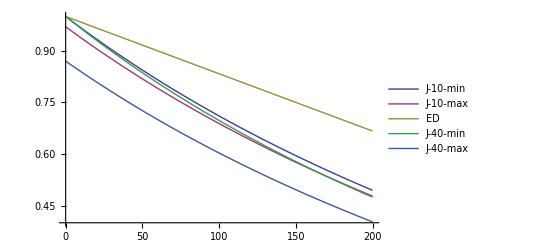

-Graphics-

```mathematica
Show[%2,ImageSize->Full]
```

```mathematica
N[maxJac[25,1000,12],10]
```

0.9506903353

```mathematica
N[minJac[25,1000,12],10]
```

0.9297560976

```mathematica
N[maxJac[250,1000,12],10]
```

0.596448749

```mathematica
N[minJac[250,1000,12],10]
```

0.5824

```mathematica
N[maxJac[25,1000,50],10]
```

0.9487704918

```mathematica
N[minJac[25,1000,50],10]
```

0.8556097561

```mathematica
N[maxJac[250,1000,50],10]
```

0.5836802664

```mathematica
N[minJac[250,1000,50],10]
```

0.5216

```mathematica
N[maxJac[100,1000,12],10]
```

0.8163452709

```mathematica
N[minJac[100,1000,12],10]
```

0.7981818182

```mathematica
N[maxJac[50,500,12],10]
```

0.814471243

```mathematica
N[minJac[50,500,12],10]
```

0.7781818182

```mathematica
minJacPct[x_,l_] := (1 - 2l - x )/(x + 1)
```

```mathematica
maxJacPct[x_,l_] := (1 - l  - x)/(x + 1- l )
```

```mathematica
L1PCT = .05
```

0.05

```mathematica
L2PCT = .2
```

0.2

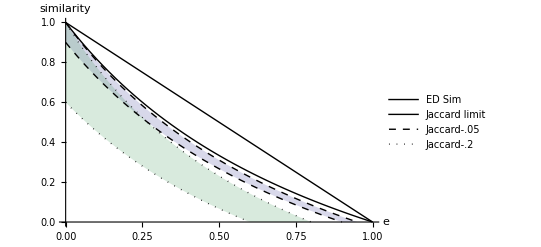

```mathematica
Plot[{maxJacPct[x,L1PCT],minJacPct[x,L1PCT],(1 - x),maxJacPct[x,L2PCT],minJacPct[x,L2PCT],(1 - x)/(1 + x)},{x,0,1}, PlotLegends-> Placed[LineLegend[{Thick,Black,{Black,Dashed},{Black,Dotted}},{"ED Sim","Jaccard limit","Jaccard-.05","Jaccard-.2"},LabelStyle->{FontFamily->"Helvetica"}],{Right,Top}],PlotRange->{{0,1},{0,1}},ImageSize-> Scaled[.9], Filling->{1->{2},4->{5}}, PlotStyle->{{Black,Dashed},{Black,Dashed},Black,{Black,Dotted},{Black,Dotted}, Black},AxesLabel->{"e","similarity"},BaseStyle->{FontSize->16}]
```

```mathematica
maxJacPct[.2, .05]
```

0.652174

```mathematica
minJacPct[.2,.05]
```

0.583333

```mathematica
list10 = {{16,0.11726},{15,0.04031},{14,0.03576},{13,0.02864},{12,0.01333},{11,0.02699},{10,0.03544},{9,0.03991},{8,0.04217}}
```

{{16,0.11726},{15,0.04031},{14,0.03576},{13,0.02864},{12,0.01333},{11,0.02699},{10,0.03544},{9,0.03991},{8,0.04217}}

```mathematica
list9 = {{14,0.09620},{13,0.07021},{12,0.04427},{11,0.05421},{10,0.07779},{9,0.08382},{8,0.08259}}
```

{{14,0.0962},{13,0.07021},{12,0.04427},{11,0.05421},{10,0.07779},{9,0.08382},{8,0.08259}}

```mathematica
list8 = {{15,0.46227},{14,0.10902},{13,0.07266},{12,0.04133},{11,0.06040},{10,0.05999},{9,0.07101}}
```

{{15,0.46227},{14,0.10902},{13,0.07266},{12,0.04133},{11,0.0604},{10,0.05999},{9,0.07101}}

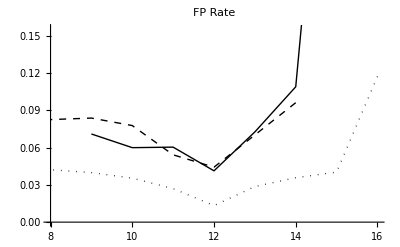

```mathematica
fp =ListPlot[{list8, list9,list10},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"FP Rate",BaseStyle->{FontSize->16}]
```

```mathematica
list10bad={{16,11368},{15,3293},{14,3069},{13,1984},{12,1228},{11,3145},{10,3541},{9,5358},{8,4709}}
```

{{16,11368},{15,3293},{14,3069},{13,1984},{12,1228},{11,3145},{10,3541},{9,5358},{8,4709}}

```mathematica
list9bad={{14,10880},{13,8231},{12,4689},{11,7945},{10,13274},{9,13538},{8,10724}}
```

{{14,10880},{13,8231},{12,4689},{11,7945},{10,13274},{9,13538},{8,10724}}

```mathematica
list8bad={{15,154661},{14,18306},{13,10106},{12,5151},{11,8596},{10,10175},{9,10590}}
```

{{15,154661},{14,18306},{13,10106},{12,5151},{11,8596},{10,10175},{9,10590}}

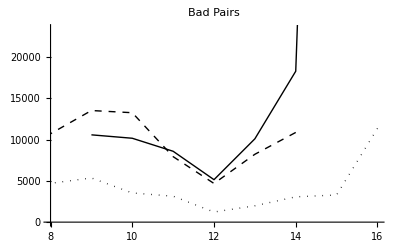

```mathematica
bd = ListPlot[{list8bad, list9bad,list10bad},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"Bad Pairs",BaseStyle->{FontSize->16}]
```

```mathematica
list10good={{16,85563},{15,78394},{14,82764},{13,67282},{12,90926},{11,113373},{10,96383},{9,128899},{8,106951}}
```

{{16,85563},{15,78394},{14,82764},{13,67282},{12,90926},{11,113373},{10,96383},{9,128899},{8,106951}}

```mathematica
list9good={{14,102220},{13,109010},{12,101233},{11,138618},{10,157360},{9,147983},{8,119127}}
```

{{14,102220},{13,109010},{12,101233},{11,138618},{10,157360},{9,147983},{8,119127}}

```mathematica
list8good={{15,179907},{14,149611},{13,128973},{12,119461},{11,133716},{10,159430},{9,138538}}
```

{{15,179907},{14,149611},{13,128973},{12,119461},{11,133716},{10,159430},{9,138538}}

```mathematica
lg =LineLegend[{Black,{Black,Dashed},{Black,Dotted}},{"k=8", "k=9","k=10"}]
```

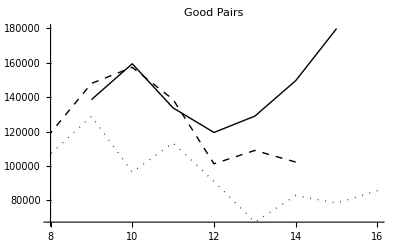

```mathematica
gd = ListPlot[{list8good, list9good,list10good},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"Good Pairs",BaseStyle->{FontSize->16}]
```

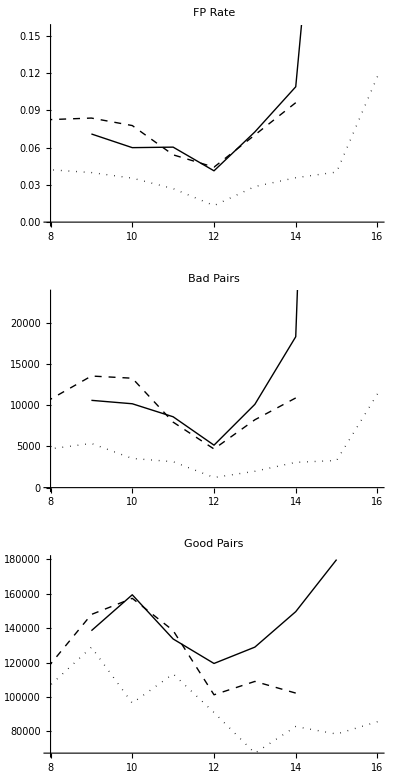

```mathematica
Legended[GraphicsGrid[{{fp},{bd},{gd}},ImageSize-> Scaled[.5]],lg]
```

```mathematica
Export["edgrid.eps",Legended[GraphicsGrid[{{fp},{bd},{gd}},ImageSize-> Scaled[.5]],lg]]
```

edgrid.eps

edgrid.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["edgrid.eps"]]]
```